```mathematica
localdir = "C:\\Users\\tramiada\\OneDrive\\Projects\\gen_spe\\Figure4\\";
```

## Figure 4 cd

### Figure 4c

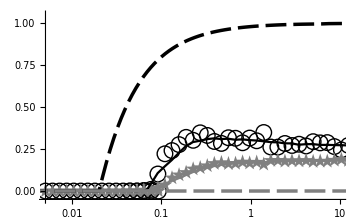

```mathematica
(*Compile data*)
data = {};
Do[
raw1 =Import[localdir<>"fig4cd\\task_4_Est_model_8_M_5_size_4_T_2000_ls_0.5_diff_a_1_muR_0.1_lambda_0.4_replicates_"<>ToString@rep<>"_w_2.csv"][[;;-3]];
raw2  =Transpose[{raw1[[All,1]],raw1[[All,2]],raw1[[All,3]],raw1[[All,4]],Mean[Transpose@raw1[[All,5;;8]]]}];
AppendTo[data,raw2];
,{rep,0,119,1}];
data2 = Mean[data];

gd =Table[{π* data2[[i,2]]^2 * data2[[i,1]]*data2[[i,3]], data2[[i,4]]},{i , Length[data2]}];
sd =Table[{π*data2[[i,2]]^2 * data2[[i,1]] *data2[[i,3]], data2[[i,5]]},{i , Length[data2]}];

gd =FlattenAt[Prepend[gd, d0xy],1];
sd =FlattenAt[Prepend[sd, d0xy],1];

fig4c = ListLogLinearPlot[{gd,sd},ImageSize->Medium,Joined-> False, PlotMarkers->pm,PlotStyle-> ps1,AxesStyle->as2,PlotRange->prange,AxesOrigin->ao] ;

gd1 = MovingAverage[gd,8] ;sd1 = MovingAverage[sd,8] ;

AppendTo[gd1, gd[[-1]]];
AppendTo[sd1, sd[[-1]]];

fig4cc =ListLogLinearPlot[{gd1,sd1},ImageSize->Medium,Joined-> True, PlotStyle->ps1,AxesStyle->as2,PlotRange->prange,AxesOrigin->ao] ;

fig4C =Show[fig4c,fig4cc,fig2e]
```

```mathematica
Export[localdir<>"fig4c.jpg",fig4C,ImageResolution->200]
```

C:\Users\tramiada\OneDrive\Projects\gen_spe\Figure4\fig4c.jpg

### Figure 4d

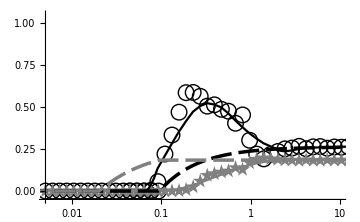

```mathematica
(*Compile data*)
data = {};
Do[
raw1 =Import[localdir<>"fig4cd\\task_4_Est_model_7_M_5_size_4_T_2000_ls_0.5_diff_a_0.8_muR_0.1_lambda_0.4_replicates_"<>ToString@rep<>"_w_2.csv"][[;;-3]];
raw2  =Transpose[{raw1[[All,1]],raw1[[All,2]],raw1[[All,3]],raw1[[All,4]],Mean[Transpose@raw1[[All,5;;8]]]}];
AppendTo[data,raw2];
,{rep,0,119,1}];
data2 = Mean[data];

gd =Table[{π* data2[[i,2]]^2 * data2[[i,1]]*data2[[i,3]], data2[[i,4]]},{i , Length[data2]}];
sd =Table[{π*data2[[i,2]]^2 * data2[[i,1]] *data2[[i,3]], data2[[i,5]]},{i , Length[data2]}];

gd =FlattenAt[Prepend[gd, d0xy],1];
sd =FlattenAt[Prepend[sd, d0xy],1];

fig4d = ListLogLinearPlot[{gd,sd},ImageSize->Medium,Joined-> False, PlotMarkers->pm,PlotStyle-> ps1,AxesStyle->as2,PlotRange->prange,AxesOrigin->ao] ;

gd1 = MovingAverage[gd,8] ;sd1 = MovingAverage[sd,8] ;

AppendTo[gd1, gd[[-1]]];
AppendTo[sd1, sd[[-1]]];

fig4dd =ListLogLinearPlot[{gd1,sd1},ImageSize->Medium,Joined-> True, PlotStyle->ps1,AxesStyle->as2,PlotRange->prange,AxesOrigin->ao] ;

fig4D =Show[fig4d,fig4dd,fig2f]
```

```mathematica
Export[localdir<>"fig4d.jpg",fig4D,ImageResolution->200]
```

C:\Users\tramiada\OneDrive\Projects\gen_spe\Figure4\fig4d.jpg

### Check with competition

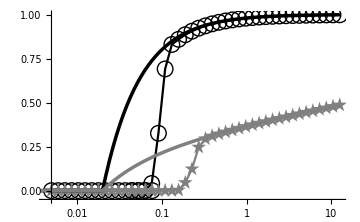

```mathematica
(*Compile data*)
data = {};
Do[
raw1 =Import["C:\\Users\\tramiada\\Documents\\Projects\\PhD project\\generalist_specialist\\Figure4\\fig4cd\\task_4_Est_model_3_M_5_size_4_T_2000_ls_0.5_diff_a_1_muR_0.1_lambda_0.4_replicates_"<>ToString@rep<>"_w_2.csv"][[;;-3]];
raw2  =Transpose[{raw1[[All,1]],raw1[[All,2]],raw1[[All,3]],raw1[[All,4]],Mean[Transpose@raw1[[All,5;;8]]]}];
AppendTo[data,raw2];
,{rep,0,39,1}];
data2 = Mean[data];

gd =Table[{π* data2[[i,2]]^2 * data2[[i,1]]*data2[[i,3]], data2[[i,4]]},{i , Length[data2]}];
sd =Table[{π*data2[[i,2]]^2 * data2[[i,1]] *data2[[i,3]], data2[[i,5]]},{i , Length[data2]}];

gd =FlattenAt[Prepend[gd, d0xy],1];
sd =FlattenAt[Prepend[sd, d0xy],1];

temp1 = ListLogLinearPlot[{gd,sd},ImageSize->Medium,Joined-> True, PlotMarkers->pm,PlotStyle-> ps1,AxesStyle->as,AxesOrigin->ao] ;

Show[temp1,fig2d]
```

### Check without difference in a

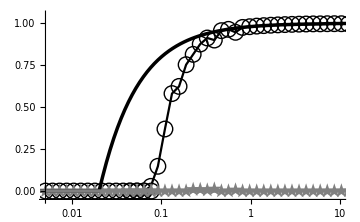

```mathematica
(*Compile data*)
data = {};
Do[
raw1 =Import["C:\\Users\\tramiada\\Documents\\Projects\\PhD project\\generalist_specialist\\Figure4\\fig4cd\\task_4_Est_model_7_M_5_size_4_T_2000_ls_0.5_diff_a_1_muR_0.1_lambda_0.4_replicates_"<>ToString@rep<>"_w_2.csv"][[;;-3]];
raw2  =Transpose[{raw1[[All,1]],raw1[[All,2]],raw1[[All,3]],raw1[[All,4]],Mean[Transpose@raw1[[All,5;;8]]]}];
AppendTo[data,raw2];
,{rep,0,39,1}];
data2 = Mean[data];

gd =Table[{π* data2[[i,2]]^2 * data2[[i,1]]*data2[[i,3]], data2[[i,4]]},{i , Length[data2]}];
sd =Table[{π*data2[[i,2]]^2 * data2[[i,1]] *data2[[i,3]], data2[[i,5]]},{i , Length[data2]}];

gd =FlattenAt[Prepend[gd, d0xy],1];
sd =FlattenAt[Prepend[sd, d0xy],1];

fig4c = ListLogLinearPlot[{gd,sd},ImageSize->Medium,Joined-> True, PlotMarkers->pm,PlotStyle-> ps1,AxesStyle->as,PlotRange->prange,AxesOrigin->ao] ;

Show[fig4c,fig2e]
```